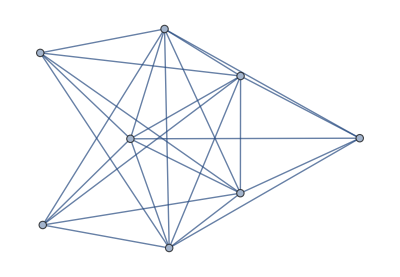
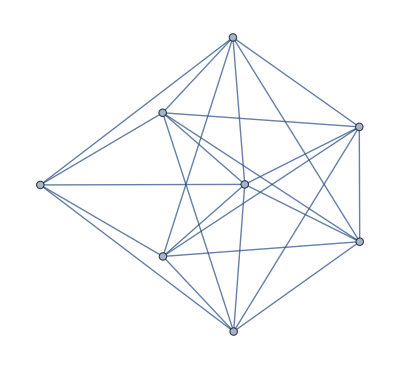
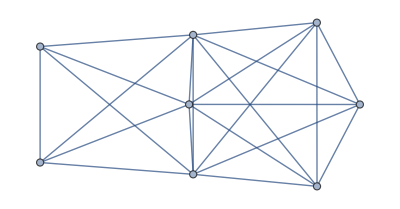
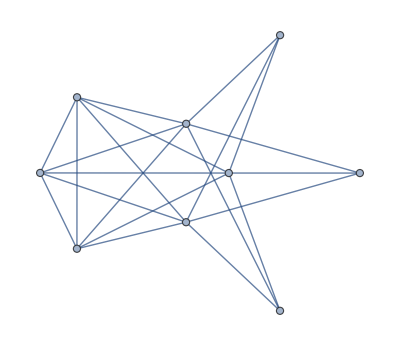
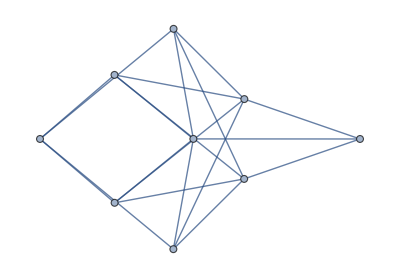
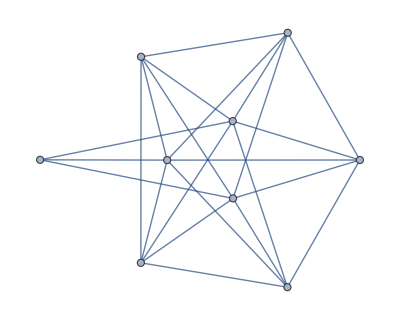
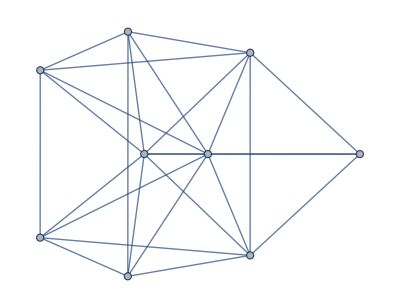
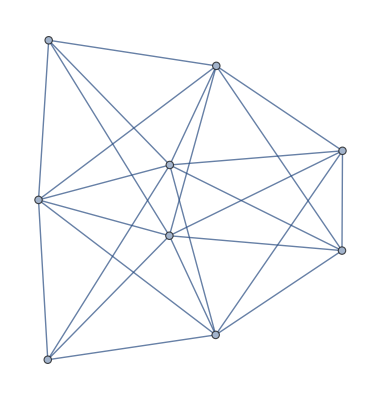
```mathematica
(*GRAPHS*)
FMList8={-Graphics-,-Graphics-,-Graphics-};
FMList9={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
MaxNilList={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
(*HELPER FUNCTIONS*)

(*IsoAppend[L,G] appends graph G to list L provided there is not a graph in L which is isomorphic to G*)
IsoAppend[L_,G_]:=If[AnyTrue[L,(H|->IsomorphicGraphQ[G,H])],L,Append[L,G]]

(*IsoUnion[L1,L2] takes the union of two lists of graphs up to isomorphism*)
IsoUnion[L1_,L2_]:=Fold[IsoAppend,L1,L2]

(*isIL[G] returns True if the graph G is intrinsically linked, False otherwise.*)
(*import the function here.*)


(*IsNonToroidalQ takes as input a graph G of order 9 and returns True if any member of NTList8 or NTList9 is a minor of G (i.e. G contains a toroidal fobidden minor) and False otherwise.*)
IsNonToroidalQ[G_]:=(AnyTrue[FMList8∪FMList9,(H|->IsomorphicSubgraphQ[H,G])])∨(AnyTrue[EdgeList[G],(e|->AnyTrue[FMList8,(H|->IsomorphicSubgraphQ[H,EdgeContract[G,e]])])])

(*NTMinorList takes as input a graph G and returns a list consisting of the members of NTList8 and NTList9 which are minors of G.*)
NTMinorList[G_]:=(Select[FMList8∪FMList9,(H|->IsomorphicSubgraphQ[H,G])])∪(Fold[IsoUnion,Map[(e|->Select[FMList8,(H|->IsomorphicSubgraphQ[H,EdgeContract[G,e]])]),EdgeList[G]]])

(*IsMaxTorNIL takes as input a graph G of order 9 and returns True if G is maximally toroidal and nIL; False otherwise.*)
IsMaxTorNIL[G_]:=!(NonToroidalQ[G]∨Quiet[isIL[G]])∧AllTrue[
Map[(e|->EdgeAdd[G,e]),EdgeList[GraphComplement[G]]],(H|->NonToroidalQ[H]∨Quiet[isIL[H]])
]
```

```mathematica
(*LEMMAS, FACTS, AND THEOREMS*)
```

```mathematica
(*This cell prints the sizes of all of the graphs in MaxNilList; note that they all have size 24, 25, or 26. This verifies Fact 2.7.*)
Map[EdgeCount,MaxNilList]
```

```mathematica
(*The following function prints out each maxnIL graph followed by a list of all the toroidal forbidden minors it contains.*)

FMinors=Map[(G|->NTMinor[G]∪NTSubgraphs[G]),MaxNilList];
Do[
Print[MaxNilList[[i]],": ",FMinors[[i]]]
,{i,Length[FMinors]}]
```

```mathematica
(*Running the previous cell shows that only four of our twenty maxnIL graphs are non-toroidal: the fourth, sixth, seventh, and tenth graphs in the list. This constitutes the proof of Lemma 2.3.
The rest of the maxnIL graphs are MTN, and have been sorted into groups below, which we invite the reader to verify.*)
```

```mathematica
MaxNilTorList={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
MaxNilNonTorList={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
(*Important also to note is that only five forbidden minors are found in these four graphs! A list is compiled below:*)
MaxNilForbMinors=Fold[Union,FMinors]
```

```mathematica
(*Even more importantly, all of these graphs have size 20:*)
Map[EdgeCount,MaxNilForbMinors]
```

```mathematica
(*By contrast, all order-8 toroidal obstructions have size 22 or higher*)Map[EdgeCount,FMList8]
```

```mathematica
(*These two cells form the proof of Lemma 2.4.*)
```

```mathematica
(*This cell forms part of the proof of Lemma 2.11*)
(*NEED TO IMPORT isIL DIRECTLY HERE BEFORE FINISHING PAPER*)
(*CONSIDER REWRITING AS AllTrue/AnyTrue/NoneTrue; may or may not improve readability*)
Lem2Point11=(
Do[(*for each graph H in S (called MaxNilForbMinors in this context)*)
H=MaxNilForbMinors[[i]];
Do[(*for each edge e in H:*)
e=EdgeList[H][[j]];
G=EdgeDelete[H,e];
isMTN=True;
Do[(*for each edge ePrime that we can add to G, excluding e:*)
ePrime=EdgeList[GraphComplement[H]][[k]];
GPrime=EdgeAdd[G,ePrime];
(*If we add an edge to G and the result is TN, then G is not MTN*)
(*Note that we need only consider the non-toroidal subgraphs of GPrime and not the minors, as the smallest order-8 obstruction has size 22*)
If[Not[Quiet[isIL[GPrime]]]∧NTSubgraphsQ[GPrime]==False,
isMTN=False;Break[]]
,{k,EdgeCount[GraphComplement[H]]}];
If[isMTN,Print[G]];
,{j,20}]
,{i,5}]
)
(*The function will print all graphs which it finds to be MTN. That this function prints nothing completes the proof of Lemma 2.11.*)
```

```mathematica
(*Function that takes in a graph G and prints out a list of subgraphs of G, which contains all MTN subgraphs of G*)
MTNSearch[G_]:=
If[EdgeCount[G]>19&&NoneTrue[MaxNilTorList,(H|->IsomorphicSubgraphQ[G,H])]&&ConnectedGraphQ[G],
If[NonToroidalQ[G],
Return[Fold[IsoUnion,Map[(e|->MTNSearch[EdgeDelete[G,e]]),EdgeList[G]]]],Return[{G}]
]
,Return[{}]
]
```

```mathematica
AbsoluteTiming[Select[Fold[IsoUnion,Map[MTNSearch,MaxNilNonTorList]],IsMaxTorNIL]]
```

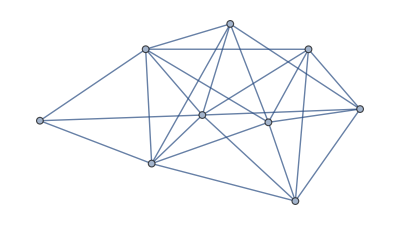
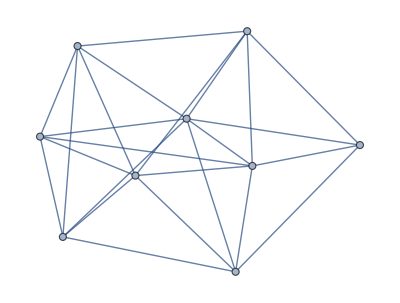
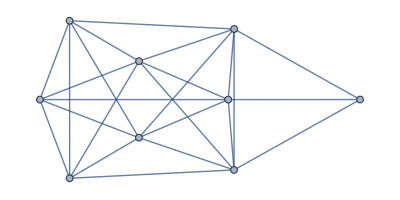
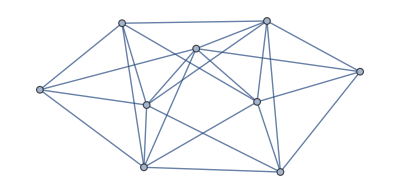
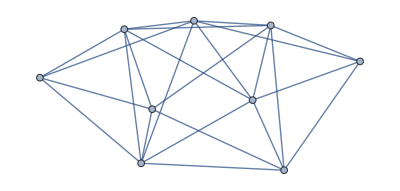
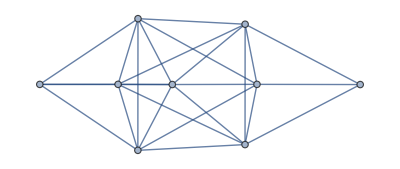
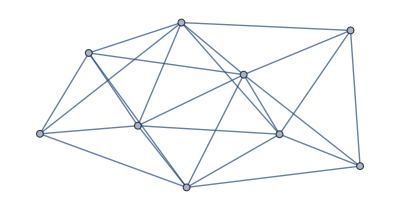
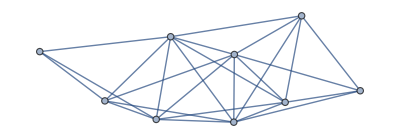
```mathematica
(*The reader may verify for themself that the above cell, after some deliberation, gives the following list of graphs:*)
ListFinal={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```